```mathematica
levelNames ={"a1","a2","b1","b2"};
```

```mathematica
rootPath = NotebookDirectory[];
```

```mathematica
texts = Table[Import[FileNameJoin[{rootPath , "\\data\\sentences\\" ,StringJoin[ x," sentences.txt"]}]],{x,levelNames}];
```

```mathematica
TextSentences[texts[[1]],4]
```

{I would like that, my dear.,I would like to order  la carte.,I would like to compose a message.,Beautiful work.}

```mathematica
sentences = Flatten[TextSentences[#,3]&@texts]
```

{I would like that, my dear.,I would like to order  la carte.,I would like to compose a message.,That’s Speedy!,Carter laughing.,Yes, that’s why.,And guess what?,Catch you later!,I think Im going
give me a break!,He couldn't even guess.,He couldn't imagine it.,Fredle couldn't resist.}

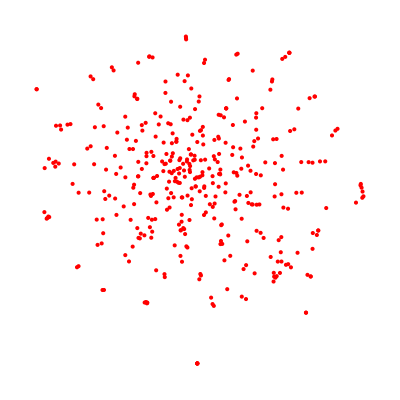

```mathematica
FeatureSpacePlot[Flatten[TextSentences[#,100]&@texts],PlotStyle->Red,LabelingFunction->Tooltip]
```

```mathematica
nSents =150;
```

```mathematica
sent2d = DimensionReduce[Flatten[TextSentences[#,nSents]&@texts],2,Method->"TSNE"];
```

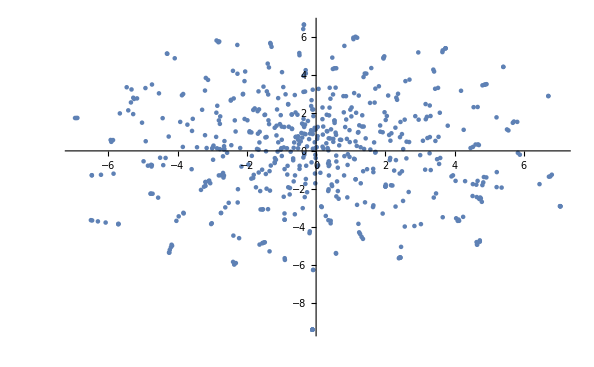

```mathematica
ListPlot[sent2d]
```